```mathematica
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
m=2;
P=2^m;
T=100-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
ΔcM=Table[0,{i,1,T}];
cMdnm=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
```

```mathematica
(Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
Do[If[BS⟦i,1⟧==AgentStrategy⟦i,1⟧,BScollect⟦i⟧=BScollect⟦i⟧+1,BScollect⟦i⟧=BScollect⟦i⟧-1],{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
ΔcM⟦t⟧=+A⟦t-1⟧*Price⟦t⟧;
cMdnm⟦t⟧=(Sum[-ΔcM⟦i⟧,{i,1,t}]+(-nM⟦t⟧*Price⟦t⟧));
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Break,Goto[begin]];)//AbsoluteTiming
```

{0.80005,Null}

```mathematica
A⟦31;;41⟧
N[Price⟦31;;41⟧,4]
N[-ΔcM⟦31;;41⟧,4]
```

{-25,-43,27,41,-61,47,-31,5,-5,7,-5}

{12.79,10.3,6.02,8.706,12.79,6.716,11.39,8.308,8.806,8.308,9.005}

{-345.2,257.5,258.9,-235.1,-524.2,409.7,-535.5,257.6,-44.03,41.54,-63.03}

```mathematica
-nM⟦31;;41⟧
N[Table[-nM⟦i⟧*Price⟦i⟧,{i,31,41}],4]
N[Table[Sum[-ΔcM⟦i⟧,{i,1,j}],{j,31,41}],4]
```

{28,3,-40,-13,28,-33,14,-17,-12,-17,-10}

{358.,30.9,-240.8,-113.2,358.,-221.6,159.5,-141.2,-105.7,-141.2,-90.05}

{-1198.,-940.6,-681.7,-916.8,-1441.,-1031.,-1567.,-1309.,-1353.,-1312.,-1375.}

```mathematica
N[cMdnm⟦31;;41⟧,4]
```

{-840.,-909.7,-922.5,-1030.,-1083.,-1253.,-1407.,-1450.,-1459.,-1453.,-1465.}

```mathematica
N[Sum[-A⟦i⟧*Price⟦i⟧,{i,1,T}],2]
```

7700.

```mathematica
N[Sum[A⟦i⟧*A⟦i⟧,{i,1,T}],2]
```

160000.

```mathematica
ListPlot[N[cMdnm,4],AxesLabel->{"t","ΣΔC_sys(t,t-1)"}]
```

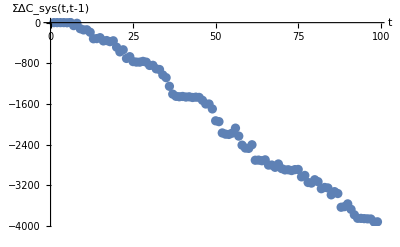

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

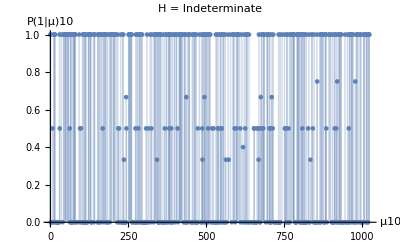

```mathematica
"P(1|μ4),P(1|μ6)";
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,Floor[T/2],T},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,Floor[T/2],T}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(T/2)*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Filling
->Axis,PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ"<>ToString[m],"P(1|μ)"<>ToString[m]},PlotLabel->"H = "<>ToString[N[H/n]]]
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

```mathematica
N[Variance[A]]
```

55.9457

```mathematica
1/(n*T)Sum[(A⟦i⟧-(Mean[A]))^2,{i,1,T}]//N
```

0.553572

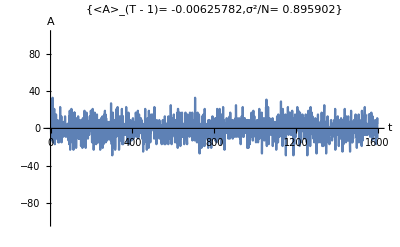

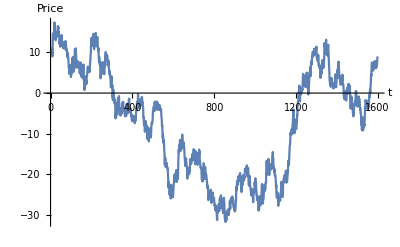

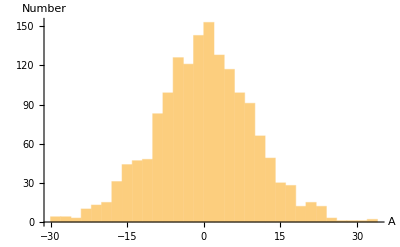

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->{"<A>_(T - 1)= "<>ToString[N[Mean[A⟦t1+1;;t2-1⟧]]],"σ^2/N= "<>ToString[N[1/n Variance[A]]]}]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

```mathematica
1/(n*T)Sum[(A⟦i⟧)^2,{i,1,n}]//N
```

0.465607

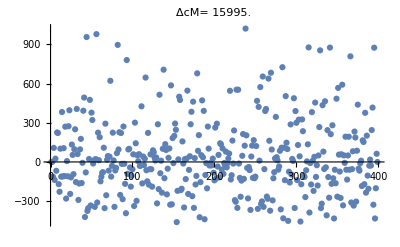

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦1;;T⟧]]]]
```

```mathematica
-Total[ΔcM⟦1;;T⟧]+(9n-nM⟦T⟧)*Price⟦T⟧-(9n*Price⟦1⟧)//N
```

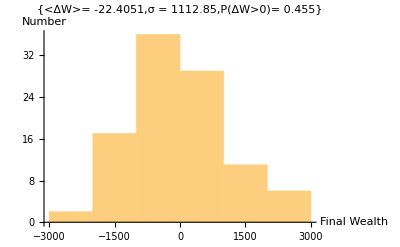

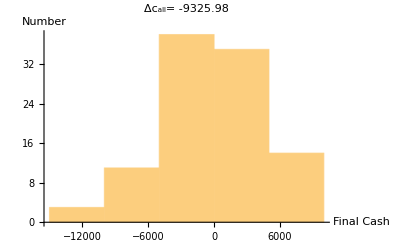

```mathematica
f4=Histogram[W⟦1;;n⟧-190,Automatic,AxesLabel->{"Final Wealth","Number"},PlotLabel->{ "<ΔW>= "<>ToString[N[Mean[W-190]]],"σ = "<>ToString[N[StandardDeviation[W-190]]],"P(ΔW>0)= "<>ToString[N[1/n Total[UnitStep[W-190]],3]]}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

11221.4

5728.73

```mathematica
c
```

{-117.913,2742.89,-6467.88,507.166,-15793.9,-7877.01,2937.71,12886.8,16011.4,5602.37,-2623.22,13986.4,8147.35,-585.691,-15287.1,-10469.4,7017.31,11421.5,-3769.09,-1811.38,-15420.,-13.6204,-12353.,-4512.65,-15424.3,-1994.65,-12016.4,-13632.5,3716.09,10951.5,7743.28,7701.99,4525.05,4759.5,-12894.1,10824.7,-8774.24,13832.5,-12025.,22391.8,7784.61,7711.14,-1155.05,3723.66,-4565.58,5531.06,12931.2,12880.6,6209.06,-12902.7,-12179.5,65.8824,-8060.59,-6415.14,-11475.,14451.6,8774.72,-16664.1,1988.24,-7848.19,-7736.45,-5882.2,8294.03,702.29,4445.94,-12353.,-6144.4,-9079.44,-15455.4,11760.8,-7721.12,16191.8,-6664.5,-11517.2,-10866.5,22351.9,485.469,-6436.84,-6529.36,10912.,-6418.1,-3852.37,-11626.9,-5141.01,-1659.12,6960.28,4652.83,-9069.69,6844.47,14452.5,-16676.,-11381.2,-2028.88,-11958.1,507.166,-4742.42,-8723.7,-15356.6,-926.169,14451.6,14442.8}